# Efficient Discovery of Halting Paths in Aggregation System Multiway Graphs

Pietro Pepe

[Affiliation]

This project investigates totalistic aggregation systems, which exhibit cellular automata behavior with an unique twist. The focus is on totalistic rules that determine cell eligibility based on the total number of active neighboring cells. By developing a simulation software using Lua and the LÖVE framework, the project enables the exploration of different rule sets and initial conditions. Multiway graphs are used to visualize the system’s behavior, and the concept of translation, rotation and reflection canonicalization simplifies the analysis of equivalent states. The project also proposes a new classification system - k-Bit rules-, systematically identifies halting states based on rules and minimal initial conditions, and uncovers insights into system growth and eventual halting. Overall, this project provides valuable insights into totalistic aggregation systems and their dynamics.

#### Code:

##### Base and helpers

```mathematica
(*Compute neighbors cells*)
NextCells[cells_List,adds_:{{1,0},{0,1},{-1,0},{0,-1}}]:=Complement[Union[Catenate[Outer[Plus,cells,adds,1]]],cells]
NextCellsMoore[cells_List] := NextCells[cells,Tuples[{-1,0,1},2]]
```

```mathematica
(*Compute quantity of active neighbors a cell has and informs if the rule accepts*)
TotalisticPruneQ[{rn_,offsets_},state_,newpos_]:=With[{
rulevec=Reverse[IntegerDigits[rn,2, Length[offsets]]]
},rulevec[[Total[Boole[MemberQ[state,newpos+#]&/@offsets]]]]==1]
```

```mathematica
(*Get List of allowed/eligible cells to be aggregated at the current step*)
NextAllowed[cells_List, rule_Integer, moore_: True] := Select[If[moore,NextCellsMoore,NextCells]@cells,TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},cells,#]&]
```

```mathematica
(*Runs external simulation software*)
RunAggSim[rule_Integer, initial_List] :=Module[{
binpath = FileNameJoin[{NotebookDirectory[],"chooser","bin","vis.exe"}]
},
Parametrize[str_] := StringJoin["\"",ToString@str,"\""];
Run @ StringRiffle[{binpath, Parametrize@rule, Parametrize@initial}," "]
]
```

```mathematica
(*Generate plot of 2D grid*)
PlotCells[cells_,opts:OptionsPattern[]]:=ArrayPlot[SparseArray[Thread[cells-Min[cells]+1->1],{Max[cells]-Min[cells]+1,Max[cells]-Min[cells]+1}],opts]
PlotCells[cells_,n_Integer,opts:OptionsPattern[]]:=ArrayPlot[SparseArray[Thread[cells+Ceiling[n/2]->1],{n,n}],opts]
PlotCellsEvent[cells_List,rule_Integer, opts:OptionsPattern[]] := EventHandler[PlotCells[cells,opts],{"MouseClicked":>RunAggSim[rule,cells]}]

ShowSteps[cells_List,start_Integer] := PlotCells[#,ImageSize->100,Mesh->True]&/@Table[Take[#,i],{i,start,Length[#]}]&@CellCanonicalize@cells
```

```mathematica
(*Execution time measurement helpers/wrappers*)
TimedEchoProcedure[proc_,timeFunc_:Timing] := With[{output = timeFunc[proc[]]},Echo[First@output,"Execution time"];Last@output]
AbsoluteTimedEchoProcedure[proc_] := TimedEchoProcedure[proc,AbsoluteTiming]

TimedProcedurePlot[proc_] := TimedEchoProcedure[proc] //
If[Length[#]==0,"No halt found",PlotCells[First[#],ImageSize->100,Mesh->True]]&
```

##### Multiway graph

```mathematica
BasePlot[graph_, plotCells_: False, graphMode_: Automatic] := Graph[graph,VertexLabels->(#->If[plotCells,PlotCells[#,ImageSize->15,Mesh->True],""]&/@VertexList[graph]),GraphLayout->graphMode,AspectRatio->1/2]
```

```mathematica
TotalisticGraph[n_Integer, rule_Integer, initial_List, plotCells_: False, moore_: True, graph_: "LayeredDigraphEmbedding"] := With[{
g = NestGraph[Function[s,Union@Append[s,#]&/@NextAllowed[s,rule,moore]],{initial},n]
},
BasePlot[g, plotCells,graph]
]
TotalisticManipulate[nmax_Integer, rule_Integer, initial_List, plotCells_: False, moore_: True, graph_: "LayeredDigraphEmbedding"] := Manipulate[
TotalisticGraph[n, rule, initial, plotCells, moore, graph],{n,0,nmax,1},SaveDefinitions->True]
```

##### Multiway graph with translation merge

```mathematica
(*Translation symmetry map*)
CellCanonicalize[state_]:=With[{m=Min/@Transpose[state]},#-m&/@state]
```

```mathematica
TotalisticCanonGraph[n_Integer, rule_Integer, initial_List, plotCells_: False, moore_: True, graph_: "LayeredDigraphEmbedding"] := With[{
g = NestGraph[Function[s,CellCanonicalize@Union@Append[s,#]&/@NextAllowed[s,rule,moore]],{CellCanonicalize@initial},n]
},
BasePlot[g, plotCells,graph]
]

TotalisticCanonManipulate[nmax_, rule_Integer:242, initial_List, plotCells_:False, moore_: True, graph_: "LayeredDigraphEmbedding"] := 
	Manipulate[
TotalisticCanonGraph[n, rule, initial, plotCells, moore, graph],{n,0,nmax,1},SaveDefinitions->True]
```

##### Multiway graph with rotation/reflection merge

```mathematica
CellCanonicalizeRotations[cells_]:=Module[{dim,mins,positive,array,canonarray},dim=Max[#]-Min[#]+1&/@Transpose[cells];
mins=Min/@Transpose[cells];
positive=#-mins+1&/@cells;
array=ReplacePart[ConstantArray[0,dim],positive->1];
canonarray=First@Sort@ResourceFunction["ArrayRotations"]@ResourceFunction["ArrayCrop"]@array;
Position[canonarray,1]-1]
```

```mathematica
TotalisticFullCanonGraph[n_Integer, rule_Integer, initial_List, plotCells_: False, moore_: True, graph_: "LayeredDigraphEmbedding"] := With[{
g = NestGraph[Function[s,CellCanonicalizeRotations@Union@Append[s,#]&/@NextAllowed[s,rule,moore]],{CellCanonicalizeRotations@initial},n]
},
BasePlot[g, plotCells,graph]
]

TotalisticFullCanonManipulate[nmax_, rule_Integer:242, initial_List, plotCells_:False, moore_: True, graph_: "LayeredDigraphEmbedding"] := 
	Manipulate[
TotalisticFullCanonGraph[n, rule, initial, plotCells, moore, graph],{n,0,nmax,1},SaveDefinitions->True]
```

##### Halting states computation

```mathematica
(* Computes list of states generated from 1 given state - list of cells *)
NextStates[rule_Integer, state_List] :=With[{neigh = Tuples[{-1,0,1},2]},If[TotalisticPruneQ[{rule,neigh},state,#],CellCanonicalizeRotations@Union@Append[state,#],Nothing]&/@NextCells[state,neigh]]

(* Computes list of all (flattened) states generated from list of states *)
NextStatesList[rule_Integer, states_List] := Union@Flatten[NextStates[rule, #]& /@ states,1]

HaltFindRaw[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3]:= NestWhile[NextStatesList[rule, #]&, {CellCanonicalizeRotations@initial}, True&, 1, maxn]
```

```mathematica
(*Compute/find minimum/first halting state*)
NextStatesListWithInfo[rule_Integer, states_List] := {Union@Flatten[#,1],states[[Flatten@Position[#,{}]]]}&@(NextStates[rule, #]& /@ states)
HaltFind[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3]:= NestWhile[NextStatesListWithInfo[rule, First[#]]&, {{CellCanonicalizeRotations@initial},{}}, Last[#]=={}&, 1, maxn]

(*Compute all halting states*)
NextStatesListWithInfoAll[rule_Integer, data_List] := With[{states = First@data},{Union@Flatten[#,1],Join[Last@data,states[[Flatten@Position[#,{}]]]]}&@(NextStates[rule, #]& /@ states)]
HaltFindAll[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3] := Nest[NextStatesListWithInfoAll[rule, #]&, {{CellCanonicalizeRotations@initial},{}}, maxn]
```

Parallelized version:

```mathematica
(*Parallelized test*)
ParallelNextStatesListWithInfo[rule_Integer, states_List] := {Union@Flatten[#,1],states[[Flatten@Position[#,{}]]]}&@ParallelMap[NextStates[rule, #]& ,states]
ParallelHaltFind[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3]:= NestWhile[ParallelNextStatesListWithInfo[rule, First[#]]&, {{CellCanonicalizeRotations@initial},{}}, Last[#]=={}&, 1, maxn]

(*Parallelized compute all halting states*)
ParallelNextStatesListWithInfoAll[rule_Integer, data_List] := With[{states = First@data},{Union@Flatten[#,1],Join[Last@data,states[[Flatten@Position[#,{}]]]]}&@ParallelMap[NextStates[rule, #]& ,states]]
ParallelHaltFindAll[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3] := Nest[NextStatesListWithInfoAll[rule, #]&, {{CellCanonicalizeRotations@initial},{}}, maxn]
```

##### Bit-Group Analysis

```mathematica
bitGroups = Function[bit,Select[Range@255,MinNeigh[#]==bit&]] /@ Range@8;

MinNeigh[rule_Integer]:=FirstPosition[Reverse@IntegerDigits[rule,2,8],1]//First
MinimalInitials[bit_Integer] := Tuples[Range[bit],2] // Subsets[#,{bit}]& // (CellCanonicalizeRotations/@#)& // Union
PlotMinimalInitials[bit_Integer]:=PlotCells[#,ImageSize->30,Mesh->True]&/@ MinimalInitials[bit]
```

```mathematica
PlotBinaryGroups[method_,bit_Integer,initial_List,maxn_Integer] := Row[ParallelTable[Labeled[PlotCells[#,ImageSize->30,Mesh->True]&/@Last@method[rn, initial,maxn]//Row[#,Spacer[3]]&,rn]//Framed,{rn,Select[Range@255,MinNeigh[#]==bit&]}],Spacer[5]]& // AbsoluteTimedEchoProcedure
```

```mathematica
PlotBinaryGroupsHalt[bit_Integer,initial_List,maxn_Integer, allHalts_: False] := PlotBinaryGroups[If[allHalts,HaltFindAll,HaltFind],bit,initial,maxn]

PlotBinaryGroupsOnlyHalt[bit_Integer,initial_List,maxn_Integer] := Select[PlotBinaryGroupsHalt[bit,initial,maxn],#[[1]]=!={}&]

(* parallel verison*)
PlotBinaryGroupsParallelHalt[bit_Integer,initial_List,maxn_Integer, allHalts_: False] := PlotBinaryGroups[If[allHalts,ParallelHaltFindAll,ParallelHaltFind],bit,initial,maxn]
```

```mathematica
TimedHaltFindPlot[rule_Integer, initial_List, maxn_Integer] := TimedProcedurePlot [Last@HaltFind[rule, initial, maxn]&]

(*Parallel case*)
TimedParallelHaltFindPlot[rule_Integer, initial_List, maxn_Integer] := TimedProcedurePlot[Last@ParallelHaltFind[rule, initial, maxn]&]
```

## Introduction

Aggregation systems are like cellular automata with a twist: once cells are set - i.e. aggregated - they remain set. The deterministic nature of standard CA is here replaced by a (standardly random) choice of what cell to add to the system, from a list of eligible cells according to the system rule.
We focus our study on totalistic rules - rules that inform if a cell is eligible based on the total number of neighbor cells active, instead of specific configurations around it.
Neighborhood  can be von Neumann (2^4  rules) or Moore(2^8  rules), even though Moore is our main focus, and all graphs and simulations will be based on it, unless explicitly mentioned otherwise.
Here is an example of a Totalistic Moore aggregation system evolution, with rule 18 (10010). This system expands to cells with 2 or 5 active neighbors (the positions of bits set in the decimal representation)
,,,,,,

Depending on the cells selected, we can get to a state where no new cell can be added, because none of them has an accepted quantity of active neighbor cells. We call this halting and is exactly what happens in the example above when we reach 
Since we have, potentially, many ways to expand the system, is natural to ponder how and when the aggregation choices affect the future of the system:

When is possible to make the system halt? When can it grow “forever”?

When does a system always halt, regardless of path/choices? When does it never halt?

“Haltable” systems always halt, that is, is there a halting path from any given state?

Our goal is to explore visualization and computation of halting states when starting from minimal initial states.

## Simulation Software

We implement a simulation software to explore any set of rules, initial conditions, with both manual and random selection of aggregated cells.
The simulation was developed with the framework LÖVE, using the Lua programming language.
Executable file and source code is available at: https://github.com/LexLoki/WSS23_AggSystems
This notebook has a desktop version that has an integration with the simulator: clicking a node in a graph launches this external simulator with that specific node state set. For it to work, the executable folder of the simulator needs to be in the same directory as the notebook file.

In this software, aggregated cells are white, and eligible cells are pink. Several halting states were found manually with the aid of the software:

-Graphics-

And also some big fancy one,from rule 4:
-Graphics-

However interesting, this simulations are done following a single path at a time, and are then far from an fully broad approach to understand and visualize these aggregation systems. So let’s get started with using Mathematica.

## Multiway graphs

Since many choices can be made, is natural to consider the multiway graph representation of these systems. These graph represent all possible states a system can assume as vertices, and viable transitions between two states as edges.

For instance, if we consider rule 255, that accepts all cells, starting with a single cell :

1 step:

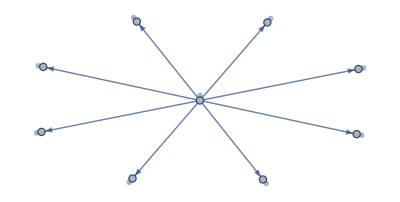

```mathematica
TotalisticGraph[1,255,{{0,0}},True,True,"SpringElectricalEmbedding"]
```

2 steps:

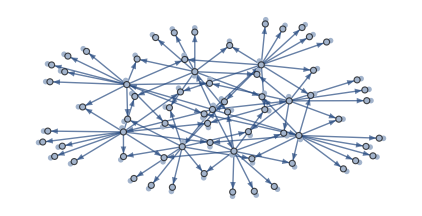

```mathematica
TotalisticGraph[2,255,{{0,0}},True,True,"SpringElectricalEmbedding"]
```

Showing these systems can grow pretty fast, although this highly varies based on the rule.
See for instance the multiway graphs of rule 2, that accepts only cells with 2 neighbors, on , for 1, 2, and 3 steps:

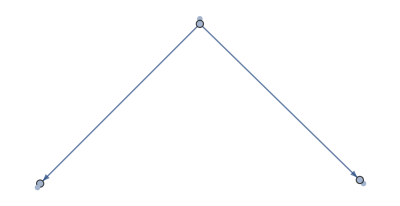
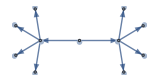
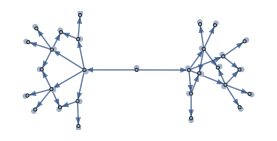

```mathematica
Row[TotalisticGraph[#,2,{{0,0},{1,1}},True,True,"SpringElectricalEmbedding"]&/@Range[3],Spacer[10]]
```

Unfortunately, rendering the graph takes a substantial amount of time, specially when generating the cells plot for each vertex:

Rule 2 execution times demonstrate that:

```mathematica
ParallelTable[TotalisticGraph[n,2,{{0,0},{1,1}},False,True]//VertexCount,{n,Range@12}]
```

{3,11,29,69,157,369,861,2017,4867,12039,30329,77021}

```mathematica
(*steps = Range@12;
MeasureTimes[plotCells_:False,moore_:True] := ParallelTable[TotalisticGraph[n,2,{{0,0},{1,1}},plotCells,moore]//Timing//First,{n,steps}]
graphTimes = MeasureTimes[False,True];
graphPlotTimes = MeasureTimes[True,True];
Grid[Transpose[{Prepend[steps,"Steps"],Prepend[graphTimes,"Graph(seconds)"], Prepend[graphPlotTimes,"Graph+cells(seconds)"]}]//Transpose,Frame->All]*)
```

-Graphics-

Another scenario, Rule 4 - only accepts cells with 3 neighbors - starting with :

```mathematica
TotalisticManipulate[6, 4, {{0,0},{1,1},{0,2}}, True, True]
```

This multiway graph seems to be growing even slower than the previous (rule 2). Is not hard to see why: this requires more neighbors active, so is natural that less cells are eligible to be added to the system.
Even though the growth is lower, computations show it also “explodes”, making it hard to study many interactions, specially when we analyze other rules.

So far we are not able to find any halting state, represented by a leaf in the multiway graph, and is hard to inspect visually as we go further.

One should note that these graphs has many states that are equivalent under translations, rotations, and reflections, and so could be collapsed/merged in single states.

### Introducing translation canonicalization

We want to apply some transformation on the set of cells that represent a state, in a way that two different sets that are equivalent under translation, i.e., by a offset, map to the same value. One simple way to do this is to translate our state to the origin. More specifically: push the minimum boundary of the grid to the origin (top left corner). This is what CellCanonicalize does.
This allows more merges in the multiway graphs. For instance:

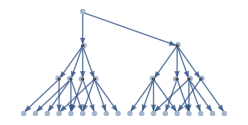
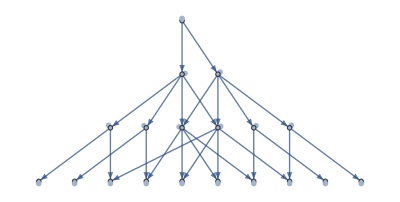
-Graphics- | -Graphics-
Rule 242 raw | Rule 242 with canon translation

```mathematica
#[3, 242, {{0,0},{1,-1}},True]&/@ {TotalisticGraph, TotalisticCanonGraph}//Grid[Transpose[{#,{"Rule 242 raw","Rule 242 with canon translation"}}]//Transpose,Frame->All]&
```

We can see how that allows us to go deeper in reading the graph:

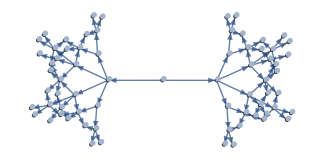
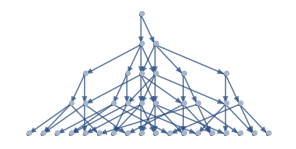
-Graphics- | -Graphics-
Rule 242 raw | Rule 242 with canon translation

```mathematica
#[4, 242, {{0,0},{1,-1}},True,True,Automatic]&/@ {TotalisticGraph, TotalisticCanonGraph} //Grid[Transpose[{#,{"Rule 242 raw","Rule 242 with canon translation"}}]//Transpose,Frame->All]&
```

The cost of performing the canonicalization is proportional to the quantity of cells of a given state. This cost is overly compensated by the amount of merges, thus reduced branching.

Rule 2 execution times demonstrate that:

```mathematica
steps = Range@12;
MeasureTimes[plotCells_:False,moore_:True] := ParallelTable[TotalisticCanonGraph[n,2,{{0,0},{1,1}},plotCells,moore]//Timing//First,{n,steps}]
graphTimes = MeasureTimes[False,True];
graphPlotTimes = MeasureTimes[True,True];
Grid[Transpose[{Prepend[steps,"Steps"],Prepend[graphTimes,"Graph(seconds)"], Prepend[graphPlotTimes,"Graph+cells(seconds)"]}]//Transpose,Frame->All]
```

Steps | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
Graph(seconds) | 0. | 0. | 0. | 0. | 0. | 0.046875 | 0.0625 | 0.109375 | 0.28125 | 0.890625 | 2.28125 | 6.70313
Graph+cells(seconds) | 0. | 0.03125 | 0.046875 | 0.078125 | 0.21875 | 0.3125 | 0.765625 | 1.54688 | 3.67188 | 8.51563 | 21.7969 | 54.6719

But we can do better, since we still got to consider degrees of symmetry.

### Introducing rotational and reflectional canonicalization

Same idea applies. The approach is to calculate, for a given state, all its 8 combinations of orthogonal rotation and reflection, and map it to the first one, given some ordering algorithm. This is achievable in Mathematica using the resource function ArrayRotation, and relying on Order, through Sort. This is what CellCanonicalizeRotation does (it also does translation).

This greatly reduces the size of the graph in most cases, specially with symmetric and small initial conditions. Is easy to see why:

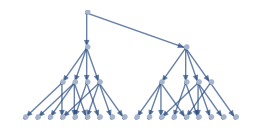
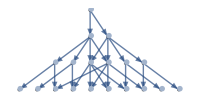
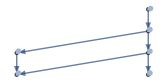
-Graphics- | -Graphics- | -Graphics-
Rule 242 raw | Rule 242 with canon translation | Rule 242 full canon

```mathematica
#[3, 242, {{0,0},{1,-1}},True, True, Automatic]&/@ {TotalisticGraph, TotalisticCanonGraph, TotalisticFullCanonGraph} //Grid[Transpose[{#,{"Rule 242 raw","Rule 242 with canon translation", "Rule 242 full canon"}}]//Transpose,Frame->All]&
```

One extra step comparing both canons:

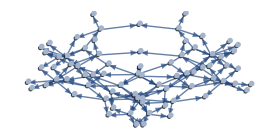
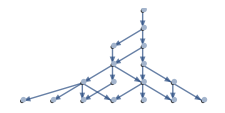
-Graphics- | -Graphics-
Rule 242 with canon translation | Rule 242 full canon

```mathematica
#[5, 242, {{0,0},{1,-1}},True,True,Automatic]&/@ {TotalisticCanonGraph, TotalisticFullCanonGraph} //Grid[Transpose[{#,{"Rule 242 with canon translation","Rule 242 full canon"}}]//Transpose,Frame->All]&
```

Rule 2 execution times are even more impressing:

```mathematica
steps = Range@12;
MeasureTimes[plotCells_:False,moore_:True] := ParallelTable[TotalisticFullCanonGraph[n,2,{{0,0},{1,1}},plotCells,moore]//Timing//First,{n,steps}]
graphTimes = MeasureTimes[False,True];
graphPlotTimes = MeasureTimes[True,True];
Grid[Transpose[{Prepend[steps,"Steps"],Prepend[graphTimes,"Graph(seconds)"], Prepend[graphPlotTimes,"Graph+cells(seconds)"]}]//Transpose,Frame->All]
```

Steps | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
Graph(seconds) | 0. | 0. | 0. | 0.015625 | 0.015625 | 0.046875 | 0.046875 | 0.15625 | 0.15625 | 0.578125 | 1.57813 | 4.53125
Graph+cells(seconds) | 0. | 0.03125 | 0.03125 | 0.015625 | 0.03125 | 0.140625 | 0.046875 | 0.375 | 0.8125 | 1.5 | 4.20313 | 10.4844

Allowing us to go even deeper.

See some other rules:

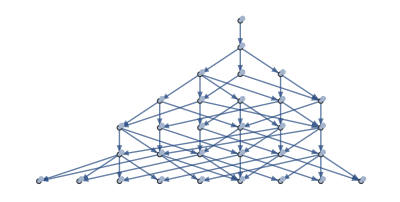
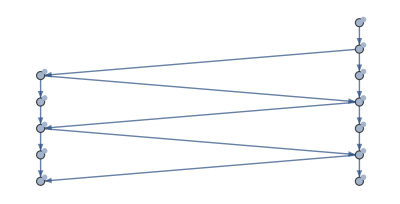
-Graphics- | -Graphics-
Rule 4 with canon translation | Rule 4 full canon

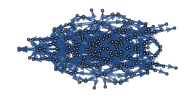
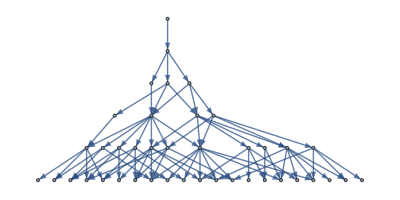
-Graphics- | -Graphics-
Rule 6 with canon translation | Rule 6 full canon

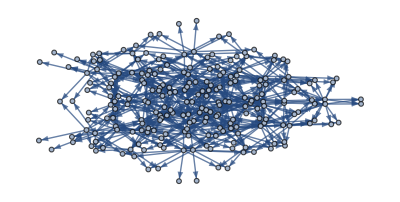
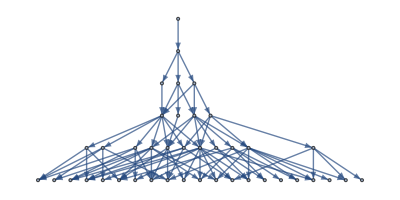
-Graphics- | -Graphics-
Rule 6 with canon translation | Rule 6 full canon

```mathematica
#[6, 4, {{0,0},{1,-1}, {2,0}},True,True,Automatic]&/@ {TotalisticCanonGraph, TotalisticFullCanonGraph} //Grid[Transpose[{#,{"Rule 4 with canon translation","Rule 4 full canon"}}]//Transpose,Frame->All]&
#[5, 6, {{0,0},{1,-1}},False,True,Automatic]&/@ {TotalisticCanonGraph, TotalisticFullCanonGraph} //Grid[Transpose[{#,{"Rule 6 with canon translation","Rule 6 full canon"}}]//Transpose,Frame->All]&
#[5, 254, {{0,0},{1,-1}},False,True,Automatic]&/@ {TotalisticCanonGraph, TotalisticFullCanonGraph} //Grid[Transpose[{#,{"Rule 6 with canon translation","Rule 6 full canon"}}]//Transpose,Frame->All]&
```

For visual exploration this is great, and with the added performance upgrade we can probably start to try to look for halting states.

## Halting states computation

Halting states can be found by looking on the multiway system graphs, like in the one for rule 18:

Execution time  0.0625

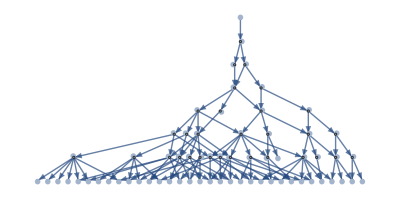

```mathematica
TotalisticFullCanonGraph[7, 18, {{0,0},{1,-1}},True, True]& // TimedEchoProcedure
```

is the only node in the tree  that leads to nowhere. And that is right: all cells in the neighborhood of this state has a number of active neighbor cells different than 2, that is the only value accepted by totalistic rule 2.

Although this state might have been easy to find, depending on the rule, and the initial state, they can be really hard (too deep) to find, sometimes even impossible. One challenge here is to be able to tell when we are not finding halting because it requires too many iterations, or because it indeed does not halt.

Moreover, an automated method to find halting states is what we look to do. It can be implemented by simply using these graphs. However, we can make it more efficient without it, since the graph, with or without the grid plots, also maps the edges. Since we are only interested about finding halts, we just need to keep the vertices, thus we can replace NestedGraph with a appropriate implementation using NestWhile and some modifications.

Trying to find same halting - rule 18 with our special method is quite simple, and of course, runs faster:

```mathematica
TimedHaltFindPlot[18,{{0,0},{1,-1}},7]
```

Execution time  0.046875

-Graphics-

And what about a harder to find halt? Rule 2 is one example where we cannot seem to find halting at depth 8:

Execution time  0.09375

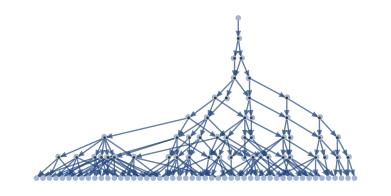

```mathematica
TotalisticFullCanonGraph[8, 2, {{0,0},{1,-1}},True, True]& // TimedEchoProcedure
```

And trying more levels than that is unfeasible. We can find it though:

```mathematica
TimedParallelHaltFindPlot[2,{{0,0},{1,-1}},11]
```

Execution time  0.25

-Graphics-

Now we are well equipped to study systematically the set of possible rules, what will be done in theory and practice (simulation) through following sections.

## Bit groups and general halting proofs

As we know, the system rules are numbers whose binary digits represent eligibility of a cell based on the quantity of its active neighbors. The less significant bit means 1 neighbor, the most significant bit means 8 neighbors. From here on, when we say Bit k, we refer to the bit of k neighbor acceptance, or then a shorthand for the acceptance.

We adopt also a distinct term: “k-Bit rule”, used to arrange our set of 255 possible rules (moore/8 connectivity) in a relevant way for our analysis, as explained below.

#### Definition: k-Bit rule: a rule where the bit k is the lower bit set, i.e., system admit cells with exactly k neighbors and possibly more, but not less. is the set of k-bit rules.

```mathematica
formattedData = Transpose @{Range@Length@bitGroups,StringJoin["(#",ToString@Length@#,"): ",StringRiffle[ToString/@#,","]]&/@ bitGroups};
Print[Grid[Prepend[formattedData,{"Bit","Bit Rules Set"}],Frame->All,Alignment->Left]];
```

Bit | Bit Rules Set
1 | (#128): 1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199,201,203,205,207,209,211,213,215,217,219,221,223,225,227,229,231,233,235,237,239,241,243,245,247,249,251,253,255
2 | (#64): 2,6,10,14,18,22,26,30,34,38,42,46,50,54,58,62,66,70,74,78,82,86,90,94,98,102,106,110,114,118,122,126,130,134,138,142,146,150,154,158,162,166,170,174,178,182,186,190,194,198,202,206,210,214,218,222,226,230,234,238,242,246,250,254
3 | (#32): 4,12,20,28,36,44,52,60,68,76,84,92,100,108,116,124,132,140,148,156,164,172,180,188,196,204,212,220,228,236,244,252
4 | (#16): 8,24,40,56,72,88,104,120,136,152,168,184,200,216,232,248
5 | (#8): 16,48,80,112,144,176,208,240
6 | (#4): 32,96,160,224
7 | (#2): 64,192
8 | (#1): 128

#### Remarks:

If all bits set in a rule  are set in a rule , the multiway-system graph of  is contained in . After all, a system with   can do all choices   can. We say   contains  .

See for instance how the multiway graphs for rule 2 (binary 10) is contained in the one for rule 6 (binary 11):

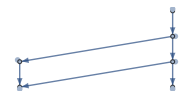
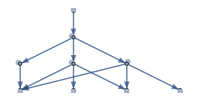

```mathematica
TotalisticFullCanonGraph[3,#,{{0,0},{1,1}},True, True]&/@{2,6} //Row[#,Spacer[8]]&
```

The lower rule in a k-Bit group is contained by all other rules in the same group. It should then be the easiest to compute.

Analogously, the higher rule (in a same group) contains all others, and then should be harder to compute.

### 4 connectivity halting lemmas:

4 connectivity was not the focus of this study, and the following simple proofs make it clear why: they are far too simple in terms of determining halting. (note that for 4 connectivity, there are only 16 rules, and 4 bit groups).

#### 1-Bit rules never halt

Proof: Let s be any given state (collection of cells). There will be a set of cells with higher horizontal coordinate. Let p be the coordinates of the cell from this set with higher vertical coordinate. The cells at positions p+{-1,1} and p+{1,1} will be unset, so the cell at p+{0,1} will have exactly one neighbor. So the system can grow with it.

#### Non 1-Bit rules always halt

Proof: Let s be any given state (collection of cells). Let r be any rectangle that contains all cells from s. A cell outside r will have, at most, 1 neighbors cell inside rUs. It is then impossible to add a cell from outside, and so the system will halt eventually
-Graphics-

### 8 connectivity lemmas:

We can use similar arguments from 4 connectivity to 8, but the conclusion results only apply to a small subset of the rules

#### 1-Bit rules never halt.

Proof: Let s be any given state (collection of cells). There will be a set of cells with higher horizontal coordinate. Let p be the coordinates of the cell from this set with higher vertical coordinate. The cell at position p+{1,1} will have exactly one neighbor. So the system can grow with it.
-Graphics-

#### ()-Bit rules always halt.

-Graphics-
Proof: Let s be any given state (collection of cells). Let r be any rectangle that contains all cells from s. A cell outside r will have, at most, 3 neighbors cell inside rUs. It is then impossible to add a cell from outside, and so the system will halt eventually

#### Now we are left with the set of 2-Bit and 3-Bit rules, 98 in total. We computationally analyze them in the following section. However there is one interesting result:

#### 2-Bit rules with bit 3 set never halt

Proof: we prove my contradiction by assuming we have a halting state, that is, a state where there are no eligible cells to insert.In this case, no cell with exactly 2 or 3 neighbors.

Assume that we have a halting state. We are going to define a “walk” along its boundary. We pick the cell to the rightest of the top row of the boundary. Like the gray cell below:
-Graphics--Graphics-
Apart from the gray corner cell, where we currently are,  in general we do not know which cells are active. Breaking up the possibilities:

If 4 is on and 5 is off, have a double corner, the cell to our right has 3 neighbors, so is eligible: contradiction

If 2 is on, the cell on our top has 2 neighbors, then is eligible: contradiction

If 4 and 5 are off, and since every cell that was added required at least 2 neighbors, cells 2 and 3 are the only possible neighbors for the corner cell. So they are on, and then our right has 2 neighbors, then is eligible: contradiction

Otherwise, we move to the bottom row, go to the rightmost cell, our new corner, and repeat the checks above.

This process is finite, because otherwise we would be moving in a down right direction infinitely, contradicting our hypothesis that we are walking on a finite boundary. Conclusion: such a halting configuration is impossible.

#### This reduces our halting study set to 64 rules.

## Bit group halt-finding analysis and results

PlotBinaryGroupsHalt gives us the list of halting states found for given rule, initial cells and maximum depth.
A k-Bit rule requires a minimum of k initial cells in order to not halt instantly (trivially). MinimalInitials provides the set of minimal initial cells for a given rule.

### 1-Bit

As we already know, we cannot halt with 1-Bit rules:

```mathematica
PlotBinaryGroupsHalt[1,{{0,0}},8]
```

{{}1,{}3,{}5,{}7,{}9,{}11,{}13,{}15,{}17,{}19,{}21,{}23,{}25,{}27,{}29,{}31,{}33,{}35,{}37,{}39,{}41,{}43,{}45,{}47,{}49,{}51,{}53,{}55,{}57,{}59,{}61,{}63,{}65,{}67,{}69,{}71,{}73,{}75,{}77,{}79,{}81,{}83,{}85,{}87,{}89,{}91,{}93,{}95,{}97,{}99,{}101,{}103,{}105,{}107,{}109,{}111,{}113,{}115,{}117,{}119,{}121,{}123,{}125,{}127,{}129,{}131,{}133,{}135,{}137,{}139,{}141,{}143,{}145,{}147,{}149,{}151,{}153,{}155,{}157,{}159,{}161,{}163,{}165,{}167,{}169,{}171,{}173,{}175,{}177,{}179,{}181,{}183,{}185,{}187,{}189,{}191,{}193,{}195,{}197,{}199,{}201,{}203,{}205,{}207,{}209,{}211,{}213,{}215,{}217,{}219,{}221,{}223,{}225,{}227,{}229,{}231,{}233,{}235,{}237,{}239,{}241,{}243,{}245,{}247,{}249,{}251,{}253,{}255}

### 2-Bit

```mathematica
Echo [PlotMinimalInitials[2],"Initial states: "];
```

Initial states:   -Graphics-,-Graphics-

#### Initial redundancy

Is easy to see that both initial states result in same configurations, regardless of the subsequent bits:

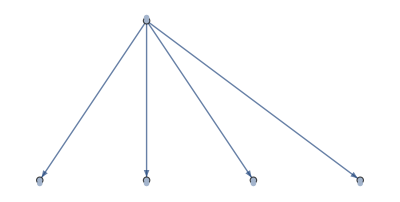
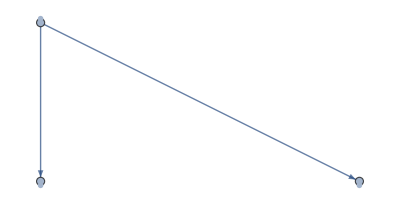

```mathematica
TotalisticGraph[1,2,#,True]& /@ MinimalInitials[2] // Row[#,Spacer[18]]&
```

#### Halting and performance

For this rule, branching factor can be substantially high.
Computing only states (no edges) with HaltFind is considerably lighter on memory and faster.
Running 11 steps in the simplest rule gives us a halting configuration:

```mathematica
TimedHaltFindPlot[First@bitGroups[[2]],First@MinimalInitials@2,11]
```

Execution time  1.25

-Graphics-

This might not seem much, however this is the simplest case for 2-Bit group, and thus represent a lower bound. Rules with more branching can get quite more expensive to run. The most complicated rule (254) from this group for instance:

```mathematica
TimedHaltFindPlot[Last@bitGroups[[2]],First@MinimalInitials@2,11]
```

Execution time  29.375

No halt found

Our parallelized implementation can improve this though:

```mathematica
TimedParallelHaltFindPlot[Last@bitGroups[[2]],First@MinimalInitials@2,11]
```

Execution time  4.85938

No halt found

Although this improves a lot the time to compute for a single rule, it does not work well to run for all the rules. Parallelizing across the 64 2-Bit rules the sequential algorithm is significantly faster then sequentially running each parallelized algorithm, and is not possible in Mathematica to nest parallelization, so we can only use one.

Let’s see the halting states we can find, up to 11 steps, for each 2-Bit rules. Our parallelized computation runs for a couple of minutes and we get:

```mathematica
(*PlotBinaryGroupsHalt[2,{{0,0},{1,1}},11, True])
```

Execution time  317.915

-Graphics-26-Graphics-1014-Graphics--Graphics--Graphics-1822-Graphics--Graphics--Graphics--Graphics-263034384246-Graphics--Graphics-5054-Graphics--Graphics--Graphics-5862-Graphics-6670-Graphics-7478-Graphics--Graphics--Graphics-8286-Graphics--Graphics--Graphics--Graphics-909498102106110-Graphics--Graphics-114118-Graphics--Graphics--Graphics-122126-Graphics-130134-Graphics-138142-Graphics--Graphics-146150-Graphics--Graphics--Graphics-154158162166170174-Graphics-178182-Graphics--Graphics-186190-Graphics-194198-Graphics-202206-Graphics--Graphics-210214-Graphics--Graphics--Graphics-218222226230234238-Graphics-242246-Graphics--Graphics-250254

Remember that some of these rules (half of them) we already proved that cannot halt.

```mathematica
FromDigits[Reverse@#,2]&/@Select[Tuples[{0,1},8],And[#[[1]]==0,#[[2]]==1, #[[3]]==1] &] // Sort // Echo[#,"Provable never halt"]&;
```

Provable never halt  {6,14,22,30,38,46,54,62,70,78,86,94,102,110,118,126,134,142,150,158,166,174,182,190,198,206,214,222,230,238,246,254}

So the rules we have not been able to determine whether or not can converge are: 34, 42, 98, 106, 162, 170, 226, 234

For the 2-Bit rules we provide some interpretation/discussion of minimal cases that appeared:

#### Subcase analysis:

Rule 2 is the lesser rule of 2-bit group, so its halting state is a state reachable by every other rule in the group. Even though all other rules can reach this state, they do not necessarily get stuck on it. The condition to halt is easy to see when we observe the boundary of the system. The 2 neighbors cells in the “side holes” require bit 6 to expand, while all others require either bits 1 or 3.
This means that having bits 3 and 6 unset makes this state a halting state. This means a quarter of the 64 cells in the 2-bit group reach this halting state:

```mathematica
FromDigits[Reverse@#,2]&/@Select[Tuples[{0,1},8],And[#[[1]]==0,#[[2]]==1, #[[3]]==0, #[[6]]==0] &] // Sort
```

{2,10,18,26,66,74,82,90,130,138,146,154,194,202,210,218}

Interestingly, for many of them, we can find a halt state with even less steps than rule 2:

#### Subcase analysis:

Is easy to see that a required condition for this state to be halting is that the rule cannot have bit 3. This is all we need to get stuck in this state (since every cell has 3 or less neighbors), but we need a little bit more to be able to get in this state. Analyzing the tree we can see how we got there:

```mathematica
Row[ShowSteps[{{1,3},{2,4},{2,3},{2,2}, {3,2},{3,1},{4,2},{3,3}},2],Spacer[1]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

The last block required bit 5 to be set. All others required only bit 2.
But what if we consider adding this last block earlier?

```mathematica
Row[ShowSteps[{{1,3},{2,4},{2,3},{2,2}, {3,2},{3,3},{3,1},{4,2}},2],Spacer[1]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

The last block required bit 3 to be set, and that is a contradiction. That means is impossible to follow this other order.
Conclusion: this halting state happens when bit 3 is unset and bit 5 is set. These rules are:

```mathematica
FromDigits[Reverse@#,2]&/@Select[Tuples[{0,1},8],And[#[[1]]==0,#[[2]]==1, #[[3]]==0, #[[5]]==1] &] // Sort
```

{18,26,50,58,82,90,114,122,146,154,178,186,210,218,242,250}

Exactly the ones seem in the group halt plot, as expected.

#### Special subcase analysis:

This state was found manually and requires 19 steps, using only bit 2 insertions.
To be halting though needs bits 3, 4, 6 unset. Having bit 7 set lets the system grow 2 steps adding the cells in the interior, and then also halts.

```mathematica
FromDigits[Reverse@#,2]&/@Select[Tuples[{0,1},8],And[#[[1]]==0,#[[2]]==1, #[[3]]==0, #[[4]]==0, #[[6]]==0] &] // Sort
```

{2,18,66,82,130,146,194,210}

These rules are a subset of the rules that reach the lesser rule halting state

### 3-Bit

```mathematica
Echo [Row[PlotMinimalInitials[3],Spacer[1]],"Initial states: "];
```

Initial states:   -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
ReducedMinimal3 = MinimalInitials[3][[{3,5,6,7,9,10}]];
Echo [Row[PlotCells[#,ImageSize->30,Mesh->True]&/@ ReducedMinimal3,Spacer[1]],"Reduced initial states: "];
```

Reduced initial states:   -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

(reduction explained in the following section)

#### Initial redundancy

##### Initials and are equivalent after 1 step

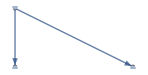
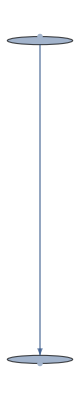

```mathematica
TotalisticGraph[1,4,#,True]& /@ MinimalInitials[3][[{1,3}]] //Row[#,Spacer@1]&
```

■ Not only that,  is different after 1 step, but after 2 steps it is also equivalent to ,

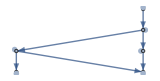
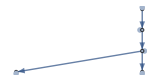

```mathematica
TotalisticFullCanonGraph[3,4,#,True]& /@ MinimalInitials[3][[{3,4}]] //Row[#,Spacer@1]&
```

■ Apart from that,  is quite trivial, since it halts after 1 step.
■   is an unique combination of 3 cells in a 3x3 grid, but is still invalid as it provides no eligible cell to be inserted.
Note that all this observations does not depend on the subsequent bits of the rule, since for these rules, first 2 steps has only 3-bit eligible cells.

#### Halting and performance

3-Bit rules has a substantially lower branching factor. We can compute several more steps than 2-Bit rules (around 10 more steps).
First we begin looking for halting with the lesser (simplest) 3-bit rule, rule 4, that we can find halting in 15 steps:

```mathematica
TimedHaltFindPlot[First@bitGroups[[3]],First@MinimalInitials@3,15]
```

Execution time  0.53125

-Graphics-

And running with the more complicated 3-bit rule, rule 252, we cannot find halting, even though we are able to run way more steps - 21:

```mathematica
TimedHaltFindPlot[Last@bitGroups[[3]],First@MinimalInitials@3,21]
```

Execution time  47.4688

No halt found

Let’s see the minimum halting states we can find, up to 11 steps, for each 3-Bit rules:

Haltings for initial:

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[1]],17, True]
```

Execution time  24.8788

-Graphics-412-Graphics-2028-Graphics-3644-Graphics-5260-Graphics-6876-Graphics-8492-Graphics-100108-Graphics-116124-Graphics-132140-Graphics-148156-Graphics-164172-Graphics-180188-Graphics-196204-Graphics-212220-Graphics-228236-Graphics-244252

Haltings for initial:

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[5]],17]
```

Execution time  99.0453

-Graphics-412-Graphics-2028-Graphics-3644-Graphics-5260-Graphics-6876-Graphics-8492-Graphics-100108-Graphics-116124-Graphics-132140-Graphics-148156-Graphics-164172-Graphics-180188-Graphics-196204-Graphics-212220-Graphics-228236-Graphics-244252

Haltings for initial:

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[6]],17]
```

Execution time  149.177

41220283644526068768492100108116124132140148156164172180188196204212220228236244252

Haltings for initial:

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[7]],17]
```

Execution time  238.189

-Graphics--Graphics-412-Graphics--Graphics--Graphics-2028-Graphics--Graphics-3644-Graphics--Graphics--Graphics-5260-Graphics--Graphics-6876-Graphics--Graphics--Graphics-8492-Graphics--Graphics-100108-Graphics--Graphics--Graphics-116124-Graphics--Graphics-132140-Graphics--Graphics--Graphics-148156-Graphics--Graphics-164172-Graphics--Graphics--Graphics-180188-Graphics--Graphics-196204-Graphics--Graphics--Graphics-212220-Graphics--Graphics-228236-Graphics--Graphics--Graphics-244252

Haltings for initial:

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[9]],17]
```

Execution time  150.67

41220283644526068768492100108116124132140148156164172180188196204212220228236244252

Haltings for initial:

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[10]],17]
```

Execution time  255.397

-Graphics--Graphics-412-Graphics--Graphics--Graphics-2028-Graphics--Graphics-3644-Graphics--Graphics--Graphics-5260-Graphics--Graphics-6876-Graphics--Graphics--Graphics-8492-Graphics--Graphics-100108-Graphics--Graphics--Graphics-116124-Graphics--Graphics-132140-Graphics--Graphics--Graphics-148156-Graphics--Graphics-164172-Graphics--Graphics--Graphics-180188-Graphics--Graphics-196204-Graphics--Graphics--Graphics-212220-Graphics--Graphics-228236-Graphics--Graphics--Graphics-244252

Is interesting that initial states have this peculiar effect in allowing halting states. Since we were not able to run further is hard to say for sure if they made the halting possible OR just made the halting possible sooner. The later seems more likely, unless some pattern created by the initial case propagates infinitely in a way that prevents otherwise halting configurations.

A look on one of these graphs show an interesting pattern of steady branching until around a 3x3 grid, and then starting to expand. See Rule 4 (binary 100) (the simplest of the group)

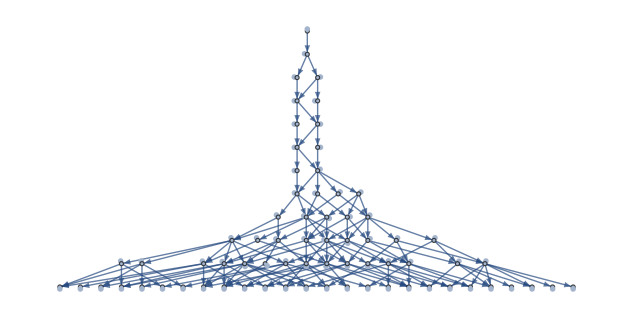

```mathematica
TotalisticFullCanonGraph[11,4,{{0,0},{1,1},{0,2}}, True]
```

## Concluding remarks

In this project, we explored totalistic aggregation systems with minimal initial conditions, which proved to be a challenging yet intriguing subset of aggregation systems. Our efforts resulted in the development of a diverse collection of visual computations for these systems, offering valuable tools for further exploration and optimization. However, due to the combinatorial nature of the problems involved, significant optimizations beyond specific purposes or systems with particular properties are unlikely.

Nonetheless, we made significant contributions to the understanding of these systems. By proposing a relevant classification of rules, we focused on a subset of 96 rules and demonstrated that 32 of them never halt, further narrowing down the “gray area for conclusions” to a group of 64 rules. Among these, 24 rules (8 2-Bit and 16 3-Bit) have yet to reveal a halting state, leaving the question open as to whether they are haltable or not. The remaining 40 rules were shown to halt, but we have not determined which of their halting configurations represent possibilities in higher branching steps of their multiway graphs.

Looking ahead, there are several promising avenues for future research:

The 16 3-Bit rules that resisted halting have a shared property that suggests they may be impossible to halt, similar to the proven non-halting nature of the 2-Bit subset. Constructing a definitive proof for this observation would be a significant step forward.

Further in-depth exploration of 2-Bit and 3-Bit rules, specially 3-Bit sensitivity to some initial configurations.

We considered an alternative halt-finding method, involving pruning subgraphs of the multiway graph that are deemed unlikely to halt soon using greedy and heuristic criteria. Although not developed in this study, it presents an intriguing approach for future investigation.

The simulator offers the capability to simulate random paths, opening up possibilities for individual “smart” path finding queries to explore and discover halting states. Developing cell selection policies for these paths could prove fruitful, providing an alternative to the classical broad-breadth search on multiway graphs.

## Keywords

[Keyword1]

[Keyword2]

....

## Acknowledgment

I would like to thank all Wolfram Staff involved in making Wolfram Summer School 2023, and for giving me this opportunity to challenge myself in this exciting environment.

Special thanks to

## References

[Ref1]

[Ref2]

...